```mathematica
S0="E4D12FB83A6C5907"
IntegerDigits[S0,2]
```

E4D12FB83A6C5907

IntegerDigits[E4D12FB83A6C5907,2]

```mathematica
base=16;
leninput=4;
lenoutput=4;

FSBOX[sbox_,input_]:=
Partition[IntegerDigits[FromDigits[sbox,base],2,lenoutput 2^leninput],lenoutput][[input+1]]

FSBOXBIN[sbox_,bininput_]:=FSBOX[sbox,FromDigits[bininput,2]]
```

```mathematica
FSBOX[S0,2]
FSBOXBIN[S0,{0,0,1,0}]
```

{1,1,0,1}

{1,1,0,1}

```mathematica
PERM={1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}
```

{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

```mathematica
SPNROUND[sbox_,perm_,bininput_]:=Module[{V,g},
(
g[x_]:=FSBOXBIN[sbox,x];
V=Flatten[Map[g,  Partition[bininput,leninput]]];
V[[perm]]

)
]
```

```mathematica
SPNROUND[S0,PERM,IntegerDigits[3,2,16]]
```

{1,1,1,0,1,1,1,0,1,1,1,0,0,0,0,1}

```mathematica
{a,b,c,d}.{e,d,h,i}
```

b d+a e+c h+d i

```mathematica
L[sbox_,a_,b_,x_]:=Mod[a.x + b.FSBOXBIN[sbox,x],2]
```

```mathematica
Table[L[S0,{0,0,1,1},{1,0,1,0},IntegerDigits[x,2,leninput]],{x,0,2^leninput-1}]
```

```mathematica
Count[{0,1,0,0,1,1,1,1,1,1,0,1,0,0,1,1},0]
```

6

```mathematica
NL[sbox_,a_,b_]:=2^leninput-Plus@@Table[L[S0,a,b,IntegerDigits[x,2,leninput]],{x,0,2^leninput-1}]
```

```mathematica
TableForm@(TNL=Table[NL[S0,IntegerDigits[a,2,leninput],IntegerDigits[b,2,lenoutput]],{a,0,2^leninput-1},{b,0,2^lenoutput-1}])
```

16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 6 | 6 | 8 | 8 | 6 | 14 | 10 | 10 | 8 | 8 | 10 | 10 | 8 | 8
8 | 8 | 6 | 6 | 8 | 8 | 6 | 6 | 8 | 8 | 10 | 10 | 8 | 8 | 2 | 10
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 10 | 2 | 6 | 6 | 10 | 10 | 6 | 6
8 | 10 | 8 | 6 | 6 | 4 | 6 | 8 | 8 | 6 | 8 | 10 | 10 | 4 | 10 | 8
8 | 6 | 6 | 8 | 6 | 8 | 12 | 10 | 6 | 8 | 4 | 10 | 8 | 6 | 6 | 8
8 | 10 | 6 | 12 | 10 | 8 | 8 | 10 | 8 | 6 | 10 | 12 | 6 | 8 | 8 | 6
8 | 6 | 8 | 10 | 10 | 4 | 10 | 8 | 6 | 8 | 10 | 8 | 12 | 10 | 8 | 10
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 6 | 10 | 10 | 6 | 10 | 6 | 6 | 2
8 | 8 | 6 | 6 | 8 | 8 | 6 | 6 | 4 | 8 | 6 | 10 | 8 | 12 | 10 | 6
8 | 12 | 6 | 10 | 4 | 8 | 10 | 6 | 10 | 10 | 8 | 8 | 10 | 10 | 8 | 8
8 | 12 | 8 | 4 | 12 | 8 | 12 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 6 | 12 | 6 | 6 | 8 | 10 | 8 | 10 | 8 | 10 | 12 | 8 | 10 | 8 | 6
8 | 10 | 10 | 8 | 6 | 12 | 8 | 10 | 4 | 6 | 10 | 8 | 10 | 8 | 8 | 10
8 | 10 | 10 | 8 | 6 | 4 | 8 | 10 | 6 | 8 | 8 | 6 | 4 | 10 | 6 | 8
8 | 6 | 4 | 6 | 6 | 8 | 10 | 8 | 8 | 6 | 12 | 6 | 6 | 8 | 10 | 8

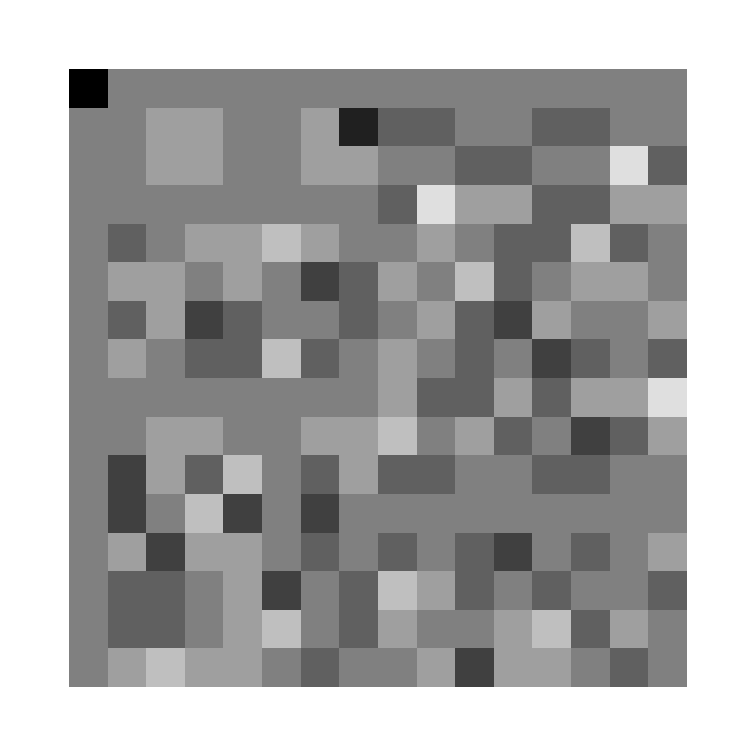

```mathematica
ArrayPlot[TNL]
```

```mathematica
Union@Flatten[ATNL=(Abs[TNL-2^(leninput-1)]/2^(leninput))]
```

{0,1/8,1/4,3/8,1/2}

```mathematica
Position[ATNL,1/8]
```

Thread::tdlen: Objects of unequal length in {{2,3},{2,4},{2,7},{2,9},{2,10},{2,13},{2,14},{3,3},{3,4},{3,7},{3,8},{3,11},{3,12},{3,16},{4,9},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{5,2},{5,4},{5,5},«3»,{5,13},{5,15},{6,2},{6,3},{6,5},{6,8},{6,9},{6,12},{6,14},{6,15},{7,2},{7,3},{7,5},{7,8},{7,10},{7,11},{7,13},{7,16},{8,2},{8,4},{8,5},{8,7},{8,9},«58»}+«1» cannot be combined.

{-1,-1}+{{2,3},{2,4},{2,7},{2,9},{2,10},{2,13},{2,14},{3,3},{3,4},{3,7},{3,8},{3,11},{3,12},{3,16},{4,9},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{5,2},{5,4},{5,5},{5,7},{5,10},{5,12},{5,13},{5,15},{6,2},{6,3},{6,5},{6,8},{6,9},{6,12},{6,14},{6,15},{7,2},{7,3},{7,5},{7,8},{7,10},{7,11},{7,13},{7,16},{8,2},{8,4},{8,5},{8,7},{8,9},{8,11},{8,14},{8,16},{9,9},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{10,3},{10,4},{10,7},{10,8},{10,11},{10,12},{10,15},{10,16},{11,3},{11,4},{11,7},{11,8},{11,9},{11,10},{11,13},{11,14},{13,2},{13,4},{13,5},{13,7},{13,9},{13,11},{13,14},{13,16},{14,2},{14,3},{14,5},{14,8},{14,10},{14,11},{14,13},{14,16},{15,2},{15,3},{15,5},{15,8},{15,9},{15,12},{15,14},{15,15},{16,2},{16,4},{16,5},{16,7},{16,10},{16,12},{16,13},{16,15}}

```mathematica
Position[ATNL,1/4]
```

```mathematica
pos=Position[ATNL,3/8]
```

{{2,8},{3,15},{4,10},{9,16}}

```mathematica
bias=Union@Flatten[ATNL=Abs[TNL/16-1/2]]
```

{0,1/8,1/4,3/8,1/2}

```mathematica
HammingWeight[x_]:=Plus@@IntegerDigits[x,2]

BestBias[sbox_]:=Module[{BestBiasAux,TNL,ATNL,bias},
(
BestBiasAux[bias_]:=Module[{pos},(
pos=Position[ATNL,bias];
SortBy[pos,HammingWeight[#[[2]]-1]&]
)];
TNL=Table[NL[sbox,IntegerDigits[a,2,leninput],IntegerDigits[b,2,lenoutput]],{a,0,2^leninput-1},{b,0,2^lenoutput-1}];
	ATNL=(Abs[TNL-2^(leninput-1)]/2^(leninput));
	bias=Drop[Union@Flatten[ATNL],1];
	Map[{#,BestBiasAux[#]}&,bias]
)]
```

```mathematica
BestBias[S0]
```

```mathematica
{{1/8,{{2,3},{2,9},{3,3},{4,9},{5,2},{5,5},{6,2},{6,3},{6,5},{6,9},{7,2},{7,3},{7,5},{8,2},{8,5},{8,9},{9,9},{10,3},{11,3},{11,9},{13,2},{13,5},{13,9},{14,2},{14,3},{14,5},{15,2},{15,3},{15,5},{15,9},{16,2},{16,5},{2,4},{2,7},{2,10},{2,13},{3,4},{3,7},{3,11},{4,11},{4,13},{5,4},{5,7},{5,10},{5,13},{7,10},{7,11},{7,13},{8,4},{8,7},{8,11},{9,10},{9,11},{9,13},{10,4},{10,7},{10,11},{11,4},{11,7},{11,10},{11,13},{13,4},{13,7},{13,11},{14,10},{14,11},{14,13},{16,4},{16,7},{16,10},{16,13},{2,14},{3,8},{3,12},{4,12},{4,14},{4,15},{5,12},{5,15},{6,8},{6,12},{6,14},{6,15},{7,8},{8,14},{9,12},{9,14},{9,15},{10,8},{10,12},{10,15},{11,8},{11,14},{13,14},{14,8},{15,8},{15,12},{15,14},{15,15},{16,12},{16,15},{3,16},{4,16},{7,16},{8,16},{10,16},{13,16},{14,16}}},{1/4,{{10,9},{11,2},{11,5},{12,2},{12,5},{13,3},{14,9},{16,3},{5,6},{6,7},{6,11},{7,4},{8,6},{8,13},{12,4},{12,7},{14,6},{15,6},{15,13},{16,11},{5,14},{7,12},{10,14},{13,12}}},{3/8,{{4,10},{2,8},{3,15},{9,16}}},{1/2,{{1,1}}}}
```

```mathematica
b0=BestBias[S0][[-2]]
b0[[1]]
b0[[2,1,2]]
```

{3/8,{{4,10},{2,8},{3,15},{9,16}}}

3/8

```mathematica
zin=zz=Table[0,{2^4}];
zin[[leninput*3+{1,2,3,4}]]=IntegerDigits[4,2,leninput];
zz[[lenoutput*3+{1,2,3,4}]]=IntegerDigits[10,2,lenoutput];
{Partition[zin,leninput],Partition[zz[[PERM]],leninput]}
```

{{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,0,0},{0,0,0,1},{0,0,0,0}}}